# Condiciones de regularidad alfa-beta

```mathematica
ff3=PowerExpand[Simplify[-(-7 r^2 α-36 β)/(36 β)-(-49 r^4 α^2+756 r^4 β)/(18 2^(2/3) β (686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3))+1/(36 2^(1/3) β)(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2+√(4 (-49 r^4 α^2+756 r^4 β)^3+(686 r^6 α^3-15876 r^6 α β-27216 c r^2 β^2-27216 r^2 α β^2)^2))^(1/3)],Assumptions->{α>0,β>0,r>0}]
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (-1944 r^2 (c+α) β^2+7 r^6 (7 α^3-162 α β)+18 √3 r^2 β √(-28 r^4 α (c+α) (7 α^2-162 β)-63 r^8 (7 α^2-144 β)+3888 (c+α)^2 β^2))^(1/3))+(7^(1/3) (-1944 r^2 (c+α) β^2+7 r^6 (7 α^3-162 α β)+18 √3 r^2 β √(-28 r^4 α (c+α) (7 α^2-162 β)-63 r^8 (7 α^2-144 β)+3888 (c+α)^2 β^2))^(1/3))/(36 β)

### Tendencia de f(r) en la región asintótica

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1+((c+α) (7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))/(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) r^2)+O[1/r]^3

```mathematica
Simplify[Solve[((c+α) (7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))/(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3))==-μ,c]];
```

Solve::ivar: -α-(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(Times[«2»]+Times[«2»]))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(Times[«2»]+Times[«2»])) (7 7^(2/3) α^2-7^(1/3) (108 Power[«2»] β+Plus[«3»]^(2/3)))) is not a valid variable.

```mathematica
c:=-α-(9 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))
```

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1-μ/r^2+O[1/r]^3

```mathematica
PowerExpand[ff3,Assumptions->{α>0,β>0,r>0}]
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)

### Región asintóticamente plana

Less::nord: Invalid comparison with 4.37499-1.22858 ⅈ attempted.

Less::nord: Invalid comparison with 8.71341-1.45562×10^-16 ⅈ attempted.

Less::nord: Invalid comparison with 2.43055-0.987793 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

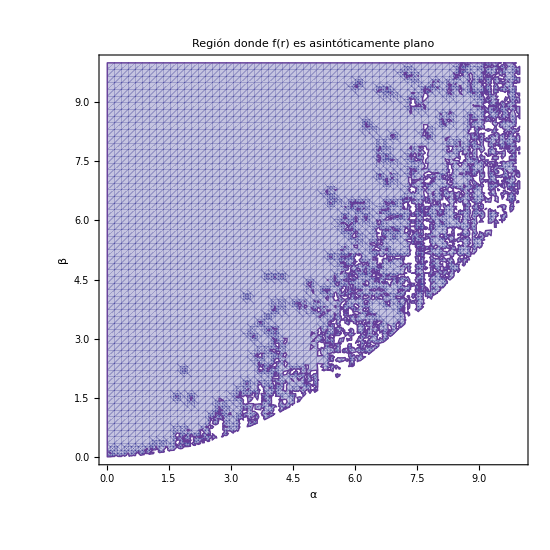

```mathematica
reg=RegionPlot[1/(36 β)(7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))<(10)^(-26),{α,0,10},{β,0,10},PlotPoints->60,Frame->True,FrameStyle->Directive[Black,1.6],FrameTicksStyle->Directive[Black,14],FrameLabel->{Style["α",20,FontFamily->"Times",Bold],Style["β",20,FontFamily->"Times",Bold]},LabelStyle->Directive[16,FontFamily->"Times"],PlotLabel->Style["Región donde f(r) es asintóticamente plano",22,Bold,FontFamily->"Times"],ImageSize->550,PlotTheme->"Classic",BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
curva=Plot[7*(α^2)/108,{α,0,10},PlotStyle->{Red,Thick}];
```

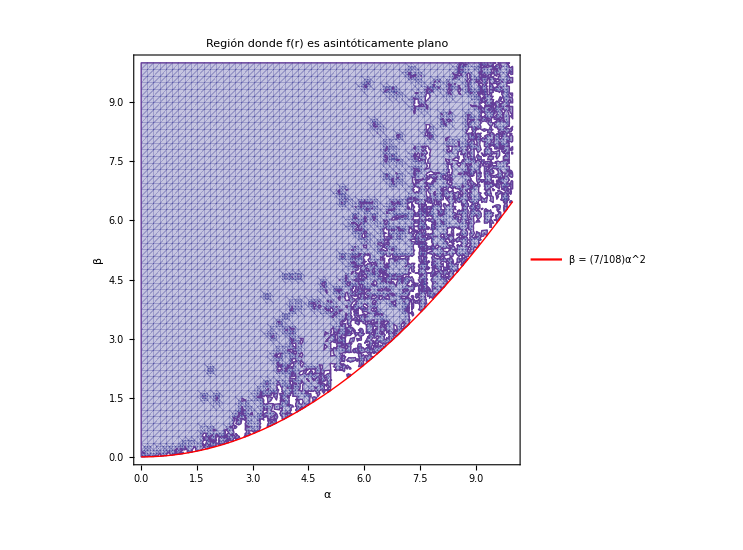

```mathematica
regajus=Legended[Show[reg,curva,PlotRange->{{0,10},{0,10}}],Placed[LineLegend[{Red},{Style["β = (7/108)α^2",16,FontFamily->"Times"]}],Right]]
```

```mathematica
Export["Restriccion de beta para asintitocamente plano.png",reg]
```

Restriccion de beta para asintitocamente plano.png

```mathematica
Export["Restriccion mas curva.png",regajus]
```

Restriccion mas curva.png

### ¿Qué ocurre si β<(7/108) α^2?

```mathematica
fmenor=Assuming[α>0&&r>0,FullSimplify[ff3/.β->(1/108)α^2]]
```

1+1/(2 α)3 r^(2/3) (14 r^(4/3)+(12 14^(2/3) r^(8/3))/(154 r^4-(17+√357) α μ+2 7^(1/6) √((-616 7^(1/6) (3 2^(2/3) (-187 ⅈ √7-415 √17) (77+ⅈ √119)^(1/3)+7^(1/6) (10727 ⅈ+2189 √119)) r^4 α μ+34 2^(1/3) (415 ⅈ-11 √119) (77+ⅈ √119)^(2/3) α^2 μ^2-476 ⅈ 2^(2/3) r^8 (-13115878279 (-3401+180 √357)+2521664915 ⅈ )^(1/3))/((-415 ⅈ+11 √119) (-12 7^(1/3)+2^(1/3) (77+ⅈ √119)^(2/3))^2)))^(1/3)+14^(1/3) (154 r^4-(17+√357) α μ+2 7^(1/6) √((-616 7^(1/6) (3 2^(2/3) (-187 ⅈ √7-415 √17) (77+ⅈ √119)^(1/3)+7^(1/6) (10727 ⅈ+2189 √119)) r^4 α μ+34 2^(1/3) (415 ⅈ-11 √119) (77+ⅈ √119)^(2/3) α^2 μ^2-476 ⅈ 2^(2/3) r^8 (-13115878279 (-3401+180 √357)+2521664915 ⅈ )^(1/3))/((-415 ⅈ+11 √119) (-12 7^(1/3)+2^(1/3) (77+ⅈ √119)^(2/3))^2)))^(1/3))

La función se vuelve imaginaria

```mathematica
Assuming[α>0&&r>0,Simplify[1/(36 β)(7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))/.β->b*α^2]]
```

(7 7^(2/3)-108 7^(2/3) b+7 (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3))/(36 b (49+54 b (-21+√21 √(-7+144 b)))^(1/3) α)

```mathematica
N[Assuming[α>0&&r>0,Simplify[(7 α-(7^(2/3) (-7+108 b) α^2)/((α^2 (-7 (-7+162 b) α+54 √21 b √((-7+144 b) α^2)))^(1/3))+7^(1/3) (α^2 (-7 (-7+162 b) α+54 √21 b √((-7+144 b) α^2)))^(1/3))/(36 b α^2)/.b->1]]]
```

-(2.5906×10^-16)/α

```mathematica
N[(7 7^(2/3)-108 7^(2/3) b+7 (49+54 b (-21+√21 √(-7+144 b)))^(1/3)+7^(1/3) (49+54 b (-21+√21 √(-7+144 b)))^(2/3))/(36 b (49+54 b (-21+√21 √(-7+144 b)))^(1/3))/.b->1000]
```

-1.78586×10^-17

```mathematica
Assuming[α>0&&β>0,Series[(7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))/(36 β),{α,0,2}]]
```

O[α]^3

```mathematica
Assuming[α>0&&β>0,Series[(7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))/(36 β),{β,Infinity,5}]]
```

O[1/β]^(13/2)

```mathematica
FullSimplify[Assuming[α>0&&β>0&&r>0,Simplify[Series[ff3,{r,Infinity,2}]]]]
```

((7 α+(7^(2/3) (7 α^2-108 β))/((49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3))+7^(1/3) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(1/3)) r^2)/(36 β)+1-μ/r^2+O[1/r]^3

### Región dentro del agujero negro

```mathematica
serieOriginal=Series[ff3,{r,0,2}];
```

```mathematica
Assuming[α>0&&β>0&&r>0&&c>0,FullSimplify[serieOriginal]]
```

1+(7 α r^2)/(36 β)+O[r]^(7/3)

```mathematica
Assuming[α>0&&β>0&&r>0&&μ>0,FullSimplify[ff3]]
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)

### Reescalado

```mathematica
fsim:=1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)
```

```mathematica
Simplify[(7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))-(7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))]
```

0

Construiremos las siguientes funciones

```mathematica
E1:=-7 α^2+144 β
B1:=49 α^3-1134 α β+54 √21 β √E1
D1:=7 √21 α^3-162 √21 α β+162 β √E1
D2:=7^(5/3) α^2-7^(1/3) (108 7^(1/3) β+B1^(2/3))
```

```mathematica
C1:=7 r^6 (7 α^3-162 α β)+((17496 r^2 β^2 √E1 (B1)^(4/3) μ)/((D1) (D2)))+18 √3 r^2 β Sqrt[(-63 r^8 (-E1)+((252 r^4 α (7 α^2-162 β) √E1 (B1)^(4/3) μ)/((D1) (D2)))+(314928 β^2 (E1) (B1)^(8/3) μ^2)/((D1)^2 (D2)^2))]
```

```mathematica
f3sim=1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (C1)^(1/3))+1/(36 β)7^(1/3) (C1)^(1/3)
```

1+(7 r^2 α)/(36 β)+(7^(2/3) r^4 (7 α^2-108 β))/(36 β (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3))+1/(36 β)7^(1/3) (7 r^6 (7 α^3-162 α β)+(17496 r^2 β^2 √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+18 √3 r^2 β √(-63 r^8 (7 α^2-144 β)+(252 r^4 α (7 α^2-162 β) √(-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(4/3) μ)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β)) (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3))))+(314928 β^2 (-7 α^2+144 β) (49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(8/3) μ^2)/((7 √21 α^3-162 √21 α β+162 β √(-7 α^2+144 β))^2 (7 7^(2/3) α^2-7^(1/3) (108 7^(1/3) β+(49 α^3-1134 α β+54 √21 β √(-7 α^2+144 β))^(2/3)))^2)))^(1/3)

```mathematica
Assuming[α>0&&β>0&&μ>0&&r>0,Simplify[fsim-f3sim]]
```

0

```mathematica
E1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[E1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
B1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[B1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
D1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
D2rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[D2/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
C1rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[C1/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
```

(-7+144 b) α^2

(49+54 b (-21+√21 √(-7+144 b))) α^3

(7 √21-162 b (√21-√(-7+144 b))) α^3

-7^(1/3) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)) α^2

-46656/49 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7 7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/49 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2))

```mathematica
f3rees=Assuming[α>0&&β>0&&r2>0&&μ>0&&b>0,Simplify[f3sim/.β->b*α^2/.r->Sqrt[(36 b α)/(7 )]r2]]
```

1+r2^2+(36 (7-108 b) b r2^4 α^2)/(7 (-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3))+1/(36 b α^2)(-46656/7 b^3 (-7+162 b) r2^6 α^6+(629856 b^3 √(-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^2 α^5 μ)/(7^(1/3) (-7 √21+162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+69984/7 b^3 r2^2 α^(9/2) √(3888/7 b^2 (-7+144 b) r2^8 α^3+(12 7^(2/3) √(-7+144 b) (-7+162 b) (49+54 b (-21+√21 √(-7+144 b)))^(4/3) r2^4 α^2 μ)/((7 √21-162 b (√21-√(-7+144 b))) (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3)))+(567 7^(1/3) (-7+144 b) (49+54 b (-21+√21 √(-7+144 b)))^(8/3) α μ^2)/((7 √21-162 b (√21-√(-7+144 b)))^2 (-7 7^(1/3)+108 7^(1/3) b+(49+54 b (-21+√21 √(-7+144 b)))^(2/3))^2)))^(1/3)

Un caso especial b=1/16

```mathematica
b:=1/16
α:=0.5
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Simplify[D2rees]
Simplify[C1rees]
Clear[b,α]
```

0.5

-0.000312518

-0.000204591

0.233111-0.00762922 ⅈ

r2^2 (-0.0113507 r2^4+(0.101702+0.190267 ⅈ) μ+0.0154102 √(0.542411 r2^8-(9.72222+18.1886 ⅈ) r2^4 μ-(108.889-162.97 ⅈ) μ^2))

Un caso interesante b=7/144. Es un caso trivial ya que la función no depende de μ

```mathematica
b:=7/144
Simplify[E1rees]
Simplify[B1rees]
Simplify[D1rees]
Simplify[D2rees]
Simplify[C1rees]
Assuming[α>0&&r2>0,FullSimplify[f3rees]]
Clear[b,α]
```

0

-(49 α^3)/8

-7/8 √21 α^3

-7/4 7^(2/3) (-1+(-1)^(2/3)) α^2

-49/512 r2^6 α^6

1+(3 r2^2)/2

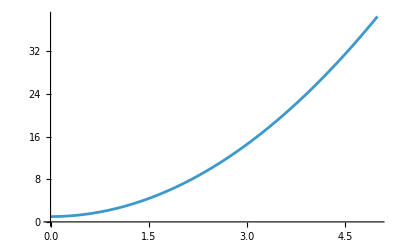

```mathematica
Plot[1+(3 r2^2)/2,{r2,0,5}]
```

### Gráficas

Variamos α y b

#### α=0.005 y b=8/108

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

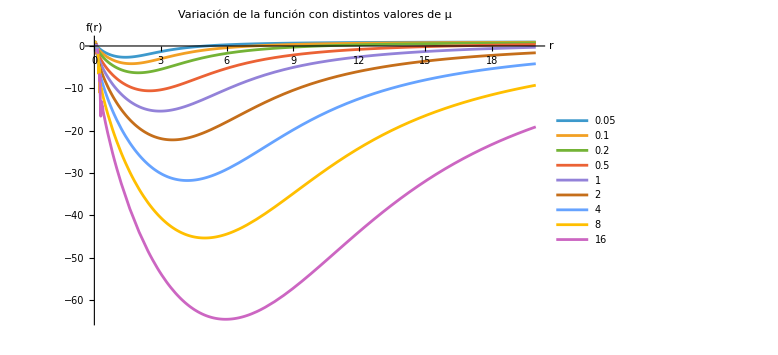

```mathematica
α:=0.005
b:=8/108
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=1/16

```mathematica
α:=0.005
b:=1/16
f3rees
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

1+r2^2+(2.00893×10^-6 r2^4)/(-7.94547×10^-14 r2^6+(7.11914×10^-11+1.33187×10^-10 ⅈ) r2^2 μ+1.07871×10^-10 r2^2 √(5.42411×10^-7 r2^8-(0.000972222+0.00181886 ⅈ) r2^4 μ-(1.08889-1.6297 ⅈ) μ^2))^(1/3)+17777.8 (-7.94547×10^-14 r2^6+(7.11914×10^-11+1.33187×10^-10 ⅈ) r2^2 μ+1.07871×10^-10 r2^2 √(5.42411×10^-7 r2^8-(0.000972222+0.00181886 ⅈ) r2^4 μ-(1.08889-1.6297 ⅈ) μ^2))^(1/3)

-Graphics-

#### α=0.005 y b=1/2

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

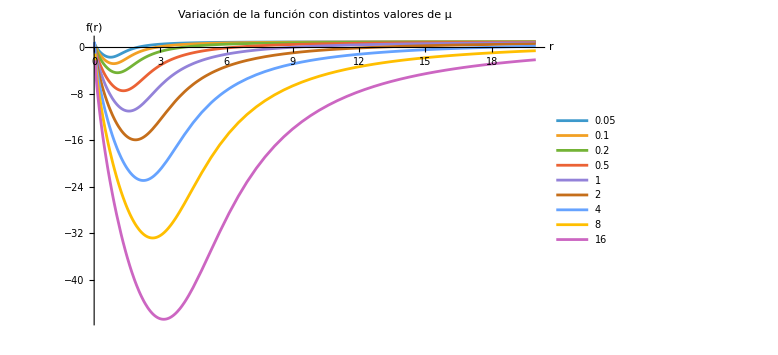

```mathematica
α:=0.005
b:=1/2
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=1

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

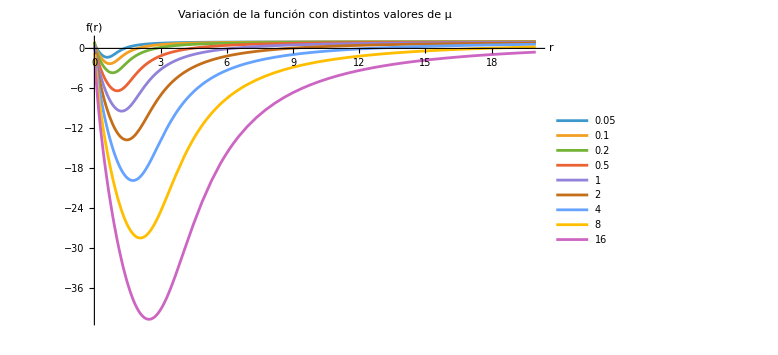

```mathematica
α:=0.005
b:=1
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=2

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

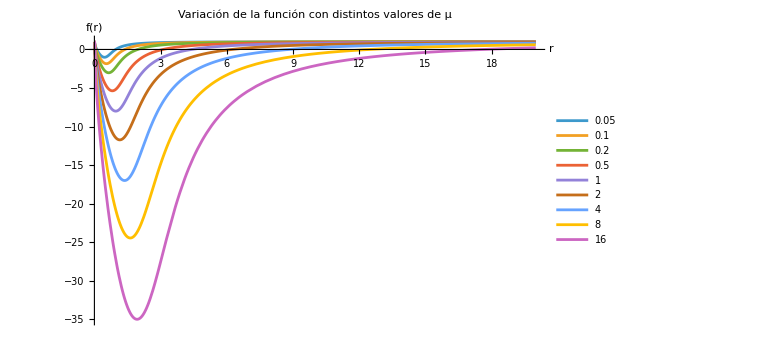

```mathematica
α:=0.005
b:=2
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=4

Power::infy: Infinite expression 1/0.^(1/3) encountered.

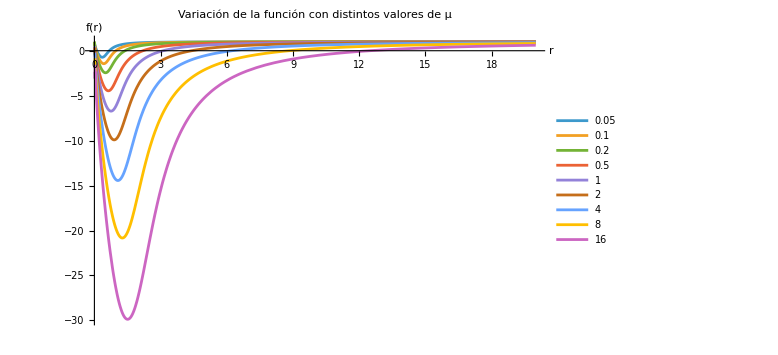

```mathematica
α:=0.005
b:=4
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.005 y b=16

Power::infy: Infinite expression 1/0.^(1/3) encountered.

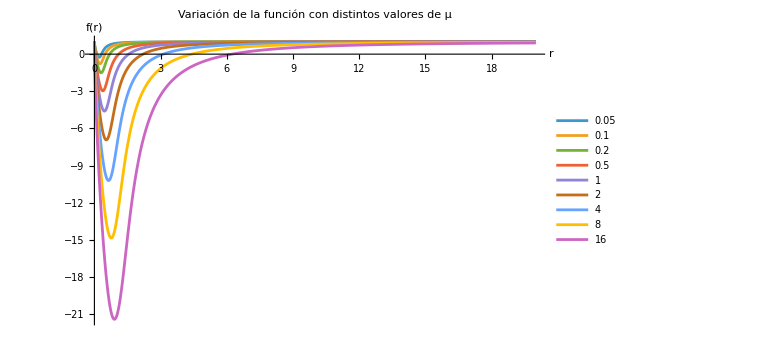

```mathematica
α:=0.005
b:=16
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```

#### α=0.01 y b=8/108

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

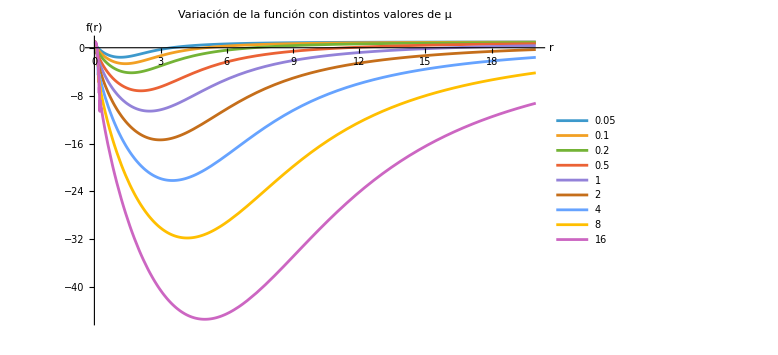

```mathematica
α:=0.01
b:=8/108
Plot[Evaluate@Table[f3rees,{μ,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,20},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ",AxesLabel->{Style["r",18,Bold],Style["f(r)",18,Bold],Style["f(r)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
Clear[α,b]
```